# Non-homogeneous 2nd order linear differential equation

```mathematica
ClearAll["Global`*"];
```

## Non-homogeneous 2nd order linear differential equation with constant coefficients and initial conditions

```mathematica
equation=y''[t]-y'[t]+y[t]==Cos[t];
```

```mathematica
initialCondition={y'[0]==0,y[0]==1};
```

```mathematica
sol=First@DSolve[{equation,initialCondition},y[t],t];
```

```mathematica
y=Chop[y[t]/.sol]
```

1/3 (3 ⅇ^(t/2) Cos[(√3 t)/2]-3 Cos[(√3 t)/2]^2 Sin[t]+√3 ⅇ^(t/2) Sin[(√3 t)/2]-3 Sin[t] Sin[(√3 t)/2]^2)

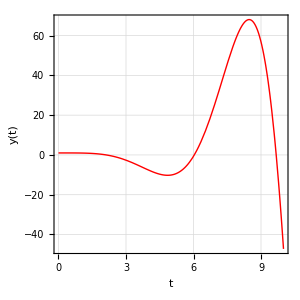

```mathematica
Plot[y,{t,0,10},
FrameLabel->{{"y(t)",None},{"t","Solution"}},
Frame->True,
GridLines->Automatic,
GridLinesStyle->Automatic,
RotateLabel->True,
PlotRange->All,
AspectRatio->1,
PlotStyle->{Thick,Red}]
```